```mathematica
(*Mn^2 Subscript[ϕ, n](x) = (Subscript[α, 1]/x+Subscript[α, 2]/(1-x))Subscript[ϕ, n](x)-β^2(∫_0)^1 dy Subscript[ϕ, n](y) PV/(y-x)^2*)
```

```mathematica
Off[General::stop];
```

```mathematica
Nx=5;
```

```mathematica
ϕ[n_][x_]:=√(α/(√π 2^n n!)) HermiteH[n,α x] E^(1/2 (-α^2) x^2)
(*ϕ[n_][x_]:=Sin[π n x];*)
```

```mathematica
α=0.5;m1=2.11;m2=2.11;β=1;λ=10^-5;
```

```mathematica
H1[n_][x_?NumberQ]:=(m1/x+m2/(1-x))ϕ[n][x];h2[m_,n_][x_?NumberQ,y_?NumberQ]:=-β^2 ϕ[m][x](ϕ[n][y])/(x-y)^2;
```

```mathematica
Table[NIntegrate[ϕ[i][x]H1[j][x]+Boole[(y>x+λ||y<x-λ)]h2[i,j][x,y]+β^2 ϕ[i][x](2ϕ[j][x])/λ,{x,0,1},{y,0,1},MaxRecursion->15],{i,1,Nx},{j,1,Nx}];
Sort@Eigenvalues[%]
```

NIntegrate::zeroregion: Integration region (1. | 1.
0 | 1) cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in x near {x,y} = {1.,0.844124}. NIntegrate obtained 39.1453 and 0.0000707913 for the integral and error estimates.

NIntegrate::zeroregion: Integration region (1. | 1.
0 | 1) cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in x near {x,y} = {1.,0.844124}. NIntegrate obtained -20.0114 and 0.000038535 for the integral and error estimates.

NIntegrate::zeroregion: Integration region (1. | 1.
0 | 1) cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

General::stop: Further output of NIntegrate::zeroregion will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in x near {x,y} = {1.,0.844124}. NIntegrate obtained -40.0193 and 0.000073899 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
Clear[α];
```

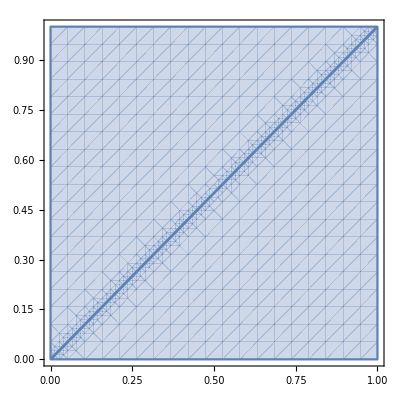

```mathematica
λ=10^-3;
region=0≤x≤1&&0≤y≤1&&(y>x+λ||y<x-λ);
RegionPlot[region,{x,0,1},{y,0,1}]
```

```mathematica
Clear[λ]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::zeroregion: Integration region (1. | 1.) cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 20 recursive bisections in x near {x} = {1.}. NIntegrate obtained 133.077 and 0.00981657 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::zeroregion: Integration region (1. | 1.) cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 20 recursive bisections in x near {x} = {1.}. NIntegrate obtained 133.077 and 0.00981657 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::zeroregion: Integration region (1. | 1.) cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

General::stop: Further output of NIntegrate::zeroregion will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 20 recursive bisections in x near {x} = {1.}. NIntegrate obtained 133.077 and 0.00981657 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.13797×10^10 and 39098.4 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -6.76086×10^10 and 342399. for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.138×10^11 and 2.90871×10^6 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

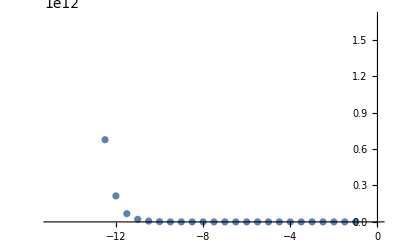

```mathematica
α=1;
ListPlot[Table[λ=10^n;{n,NIntegrate[ϕ[#1][x]H1[#2][x]+Boole[(y>x+λ||y<x-λ)]h2[#1,#2][x,y]+β^2 ϕ[#1][x](2ϕ[#2][x])/λ,{x,0,1},{y,0,1},MaxRecursion->15]&[5,5]},{n,-1,-15,-0.5}]]
Clear[α];
```

```mathematica
α=1;
NIntegrate[ϕ[#1][x]H1[#2][x]+Boole[(y>x+λ||y<x-λ)]h2[#1,#2][x,y]+β^2 ϕ[#1][x](2ϕ[#2][x])/λ,{x,0,1},{y,0,1},MaxRecursion->15]&[5,5]
Clear[α];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::zeroregion: Integration region (1. | 1.
0 | 1) cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in x near {x,y} = {1.,0.844124}. NIntegrate obtained 2.87231 and 5.29549×10^-6 for the integral and error estimates.

2.87231

```mathematica
Quit[]
```